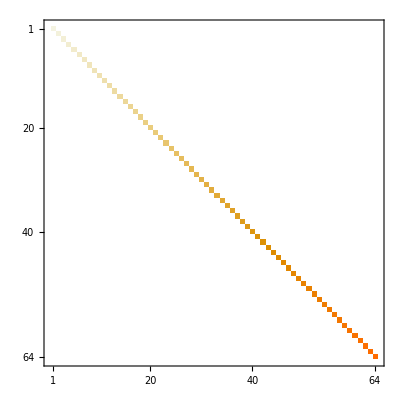

```mathematica
ClearALL["Global`*"];
SetDirectory[NotebookDirectory[]];
HName= "QHO";(*Set input file*)
Inp=FileNameJoin["H_"<>HName<>".txt"]; (*Define input*)
H=Import[Inp,"Table"]; (*Get matrix*)
MatrixPlot[H]
```

```mathematica
(*Define Pauli matrices and create list*)
X={{0,1},{1,0}};
Y={{0,-ⅈ},{ⅈ,0}};
Z={{1,0},{0,-1}};
Id=IdentityMatrix[2];
PMs={X,Y,Z,Id};
(*Get #qubits from H*)
Q=Log[2,Dimensions[H][[1]]];
```

```mathematica
plist=Tuples[PMs,{Q}];(*Create list of products*)plistStr=Tuples[{"X","Y","Z","I"},{Q}];(*String list of products*)OutpName=FileBaseName["paulis_"<>HName]<>"."<>FileExtension[Inp];
Outp=OpenWrite[OutpName];(*Create output file and open it*)len=Length[plist];
Str="";
(*Write a loop to check every plist element for Kronecker product*)
Monitor[For[j=1,j≤len,j++,σ=KroneckerProduct@@plist[[j]];
cf=Chop[Evaluate[Tr[σ.H]/2^Q]];
If[cf≠0,Str=StringJoin[Str,""<>plistStr[[j]]<>" "<>ToString[DecimalForm[Re[cf],{3,1}]]<>"+"<>ToString[0.]<>"j \n"];]];,(j/4^Q)*100//N]
Str=StringJoin[Str, " "]
Str=StringDrop[Str,-2];
WriteString[Outp,Str];
Close[Outp];
```

ZIIIII -16.0+0.j 
IZIIII -8.0+0.j 
IIZIII -4.0+0.j 
IIIZII -2.0+0.j 
IIIIZI -1.0+0.j 
IIIIIZ -0.5+0.j 
IIIIII 32.0+0.j

```mathematica
Eigensystem[KroneckerProduct[X,KroneckerProduct[Y,Y]]]
```

{{-1,-1,-1,-1,1,1,1,1},{{1,0,0,0,0,0,0,1},{0,-1,0,0,0,0,1,0},{0,0,-1,0,0,1,0,0},{0,0,0,1,1,0,0,0},{-1,0,0,0,0,0,0,1},{0,1,0,0,0,0,1,0},{0,0,1,0,0,1,0,0},{0,0,0,-1,1,0,0,0}}}

```mathematica
Eigensystem[KroneckerProduct[X,KroneckerProduct[X,X]]]
```

{{-1,-1,-1,-1,1,1,1,1},{{-1,0,0,0,0,0,0,1},{0,-1,0,0,0,0,1,0},{0,0,-1,0,0,1,0,0},{0,0,0,-1,1,0,0,0},{1,0,0,0,0,0,0,1},{0,1,0,0,0,0,1,0},{0,0,1,0,0,1,0,0},{0,0,0,1,1,0,0,0}}}